### Dynamical Systems TIF155/FIM770 Konstantinos Zakkas Problem set 1

### 1.1 Imperfect transcritical bifurcation

```mathematica
f[x_,h_,r_]:=h+x(r-x)
fDot[x_,r_]:=r -2x
sol1 = Solve[fDot[x,r] ==0,x]
```

{{x→r/2}}

### c)

```mathematica
sol2 = Solve[f[x/.sol1,h,r]==0,h]
```

{{h→-r^2/4}}

### a)

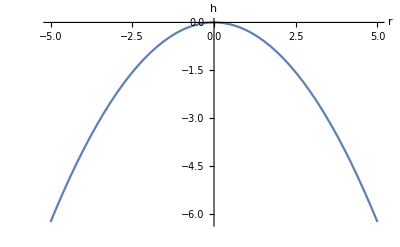

```mathematica
Plot[h/.sol2,{r,-5,5},AxesLabel->{"r","h"}]
```

### b)

```mathematica
roots = Solve[f[x,h,r] ==0,x]
```

{{x→1/2 (r-√(4 h+r^2))},{x→1/2 (r+√(4 h+r^2))}}

```mathematica
root1[h,r] := x/.roots[[1]]
root2[h,r]:= x/.roots[[2]]
Plot3D[{root1[h,r],root2[h,r]},{h,-10,10},{r,-10,10},AxesLabel->{"h","r", "x"},PlotLabel->"Fixed Point Surface"]
```

-Graphics3D-